## Define Models, Give Basic Example

```mathematica
(* Defining parameters *)
poppars={n1->500.,n2->500.};
sirpars={β1->2.1,β2->.5,γ->1};
(* Aligning Movement parameters *)
tarpars= {ϕ1->1/5., τ12 ->1/3.,ϕ2->1/20.,τ21 ->1/3.};
movtar ={0 == - ϕ1 n11 + τ12 n12,
0 == - ϕ2 n22+ τ21  n21,
(* Normalize to the residence populations *)
n11 + n12 == n1,
n22 + n21 == n2
};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
mtar ={m12-> (τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2,m21->(τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
```

```mathematica
(* This is the TaR model *)
TarVars = {s11[t],s12[t],s22[t],s21[t],i11[t],i12[t],i22[t],i21[t],r11[t],r12[t],r22[t],r21[t]};
sirTar ={
D[s11[t],t]== -β1(i11[t] + i21[t])/(s11[t]+i11[t]+r11[t]+s21[t]+i21[t]+r21[t])s11[t]- ϕ1 s11[t] + τ12 s12[t],
D[s12[t],t]== -β2(i22[t] + i12[t])/(s22[t]+i22[t]+r22[t]+s12[t]+i12[t]+r12[t])s12[t]+ ϕ1 s11[t] - τ12 s12[t],
D[s22[t],t]== -β2(i22[t] + i12[t])/(s22[t]+i22[t]+r22[t]+s12[t]+i12[t]+r12[t])s22[t]-ϕ2 s22[t] + τ21 s21[t],
D[s21[t],t]==-β1(i11[t] + i21[t])/(s11[t]+i11[t]+r11[t]+s21[t]+i21[t]+r21[t])s21[t]+ ϕ2 s22[t] - τ21 s21[t],
D[i11[t],t]== β1(i11[t] + i21[t])/(s11[t]+i11[t]+r11[t]+s21[t]+i21[t]+r21[t])s11[t] - γ i11[t] - ϕ1 i11[t] + τ12 i12[t],
D[i12[t],t]== β2(i22[t] + i12[t])/(s22[t]+i22[t]+r22[t]+s12[t]+i12[t]+r12[t])s12[t]- γ i12[t] + ϕ1 i11[t] - τ12 i12[t],
D[i22[t],t]== β2(i22[t] + i12[t])/(s22[t]+i22[t]+r22[t]+s12[t]+i12[t]+r12[t])s22[t] - γ i22[t] - ϕ2 i22[t] + τ21 i21[t],
D[i21[t],t]== β1 (i11[t] + i21[t])/(s11[t]+i11[t]+r11[t]+s21[t]+i21[t]+r21[t])s21[t] - γ i21[t] + ϕ2 i22[t] - τ21 i21[t],
D[r11[t],t]==γ i11[t]- ϕ1 r11[t] + τ12 r12[t],
D[r12[t],t]==γ i12[t]+ ϕ1 r11[t] - τ12 r12[t],
D[r22[t],t]==γ i22[t] - ϕ2 r22[t]+ τ21 r21[t],
D[r21[t],t]==γ i21[t] + ϕ2 r22[t]- τ21 r21[t]
};
```

```mathematica
(* And the flux model *) 
stvec = {S1[t],S2[t]};
itvec = {I1[t],I2[t]};
rtvec = {R1[t],R2[t]};
nvec = {n1,n2};
βvec = {β1,β2};
fij = {{0,f12},{f21,0}};
sirFlux = Table[Flatten[{D[stvec,t],D[itvec,t],D[rtvec,t]}][[j]]==Flatten[{-βvec itvec stvec/nvec + Transpose[fij].stvec - fij.{1,1}*stvec,
+ βvec itvec stvec/nvec + Transpose[fij].itvec - fij.{1,1}*itvec - γ itvec,
γ itvec+ Transpose[fij].rtvec - fij.{1,1}*rtvec}][[j]],{j,1,6}];
(*sirFlux/.sirpars/.poppars/.fluxpars//MatrixForm*)
```

```mathematica
(* Solving the TaR model *)
qTar = NDSolve[Flatten[{sirTar,
{s11[0]==n1-1,s12[0]==0,s22[0]==n2-1,s21[0]==0,
i11[0]==1,i12[0]==0,i22[0]==1,i21[0]==0,
r11[0]==0,r12[0]==0,r22[0]==0,r21[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars,
TarVars,
{t,0,10000}];
```

```mathematica
(* Solving the Flux model *)
qFlux=NDSolve[Flatten[{sirFlux,
{S1[0]==n1-1,S2[0]==n2-1,I1[0]==1,I2[0]==1,R1[0]==0,R2[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars,
Flatten[{stvec,itvec,rtvec}],
{t,0,10000}];
```

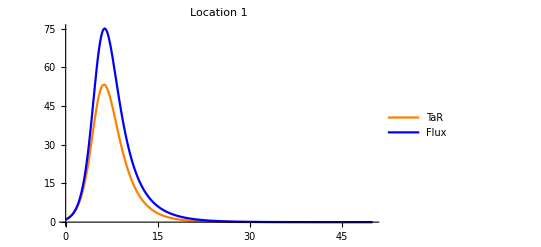

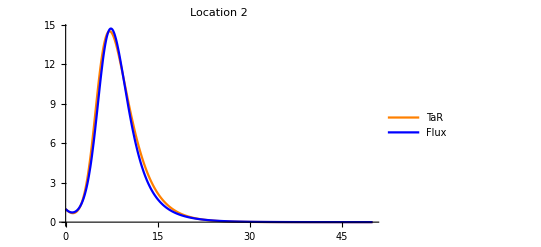

```mathematica
(* Plotting results for the TaR model and the Flux Model *)Plot[{(i11[t]+i12[t])/.qTar,I1[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 1",PlotLegends->{"TaR","Flux"}]
Plot[{(i22[t]+i21[t])/.qTar,I2[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 2",PlotLegends->{"TaR","Flux"}]
```

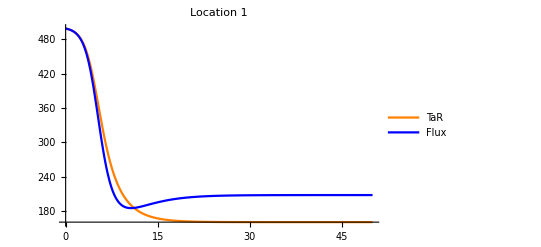

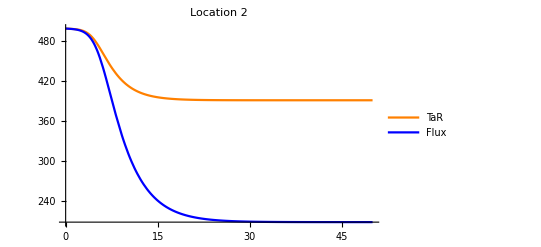

```mathematica
Plot[{(s11[t]+s12[t])/.qTar,S1[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 1",PlotLegends->{"TaR","Flux"}]
Plot[{(s22[t]+s21[t])/.qTar,S2[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 2",PlotLegends->{"TaR","Flux"}]
```

The other type of figure we’ll make: plot S0 vs. β1, comparable to the other figure made for the SIS model

```mathematica
poppars={n1->500.,n2->500.};
sirpars={γ->1.};
tarpars=  {ϕ1->.5, τ12 ->40,ϕ2->.5,τ21 ->40};
```

```mathematica
tabdat =Table[qFlux=NDSolve[Flatten[{sirFlux,
{S1[0]==n1-1,S2[0]==n2-1,I1[0]==1,I2[0]==1,R1[0]==0,R2[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->2.5},
Flatten[{stvec,itvec,rtvec}],
{t,0,10000}];
qTar = NDSolve[Flatten[{sirTar,
{s11[0]==n1-1,s12[0]==0,s22[0]==n2-1,s21[0]==0,
i11[0]==1,i12[0]==0,i22[0]==1,i21[0]==0,
r11[0]==0,r12[0]==0,r22[0]==0,r21[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->2.5},
TarVars,
{t,0,10000}];
{i,(s11[t]+s12[t])/.qTar[[1]]/.t->10000,S1[t]/.qFlux[[1]]/.t->10000},
{i,0,3,.01}];
```

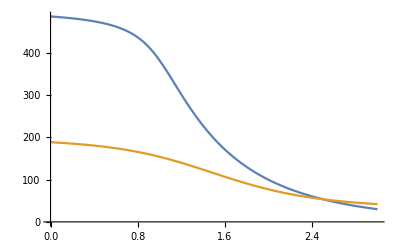

```mathematica
ListLinePlot[{tabdat[[;;,{1,2}]],tabdat[[;;,{1,3}]]}]
```

# (Upper Left) High Freq Travel; High L2 Β

```mathematica
poppars={n1->500.,n2->500.};
sirpars={γ->1.};
(* High Frequency Travel *) 
tarpars=  {ϕ1->1, τ12 ->10,ϕ2->1,τ21 ->10};
```

## First : solve for residual population size as a function of β

```mathematica
datFastHigh =Table[qFlux=NDSolve[Flatten[{sirFlux,
{S1[0]==n1-1,S2[0]==n2-1,I1[0]==1,I2[0]==1,R1[0]==0,R2[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->2.5},
Flatten[{stvec,itvec,rtvec}],
{t,0,10000}];
qTar = NDSolve[Flatten[{sirTar,
{s11[0]==n1-1,s12[0]==0,s22[0]==n2-1,s21[0]==0,
i11[0]==1,i12[0]==0,i22[0]==1,i21[0]==0,
r11[0]==0,r12[0]==0,r22[0]==0,r21[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->2.5},
TarVars,
{t,0,10000}];
{i,(s11[t]+s12[t])/.qTar[[1]]/.t->10000,S1[t]/.qFlux[[1]]/.t->10000},
{i,0,3,.01}];
```

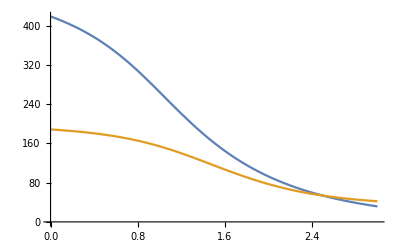

```mathematica
(* Residual population size *)
ListLinePlot[{datFastHigh[[;;,{1,2}]],datFastHigh[[;;,{1,3}]]}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Fast_high.csv",datFastHigh]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Fast_high.csv

## Second : show one archetypal set of curves

```mathematica
i = 1.5;
qFlux=NDSolve[Flatten[{sirFlux,
{S1[0]==n1-1,S2[0]==n2-1,I1[0]==1,I2[0]==1,R1[0]==0,R2[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->2.5},
Flatten[{stvec,itvec,rtvec}],
{t,0,10000}];
qTar = NDSolve[Flatten[{sirTar,
{s11[0]==n1-1,s12[0]==0,s22[0]==n2-1,s21[0]==0,
i11[0]==1,i12[0]==0,i22[0]==1,i21[0]==0,
r11[0]==0,r12[0]==0,r22[0]==0,r21[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->2.5},
TarVars,
{t,0,10000}];
```

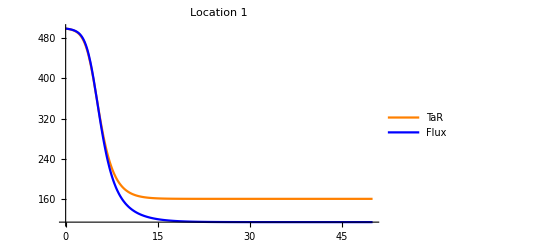

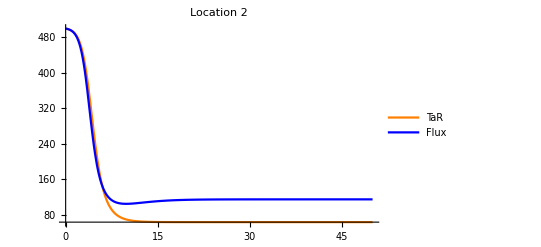

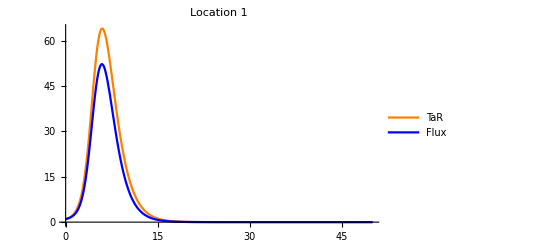

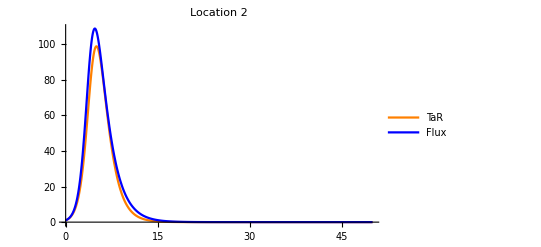

```mathematica
Plot[{(s11[t]+s12[t])/.qTar,S1[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 1",PlotLegends->{"TaR","Flux"}]
Plot[{(s22[t]+s21[t])/.qTar,S2[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 2",PlotLegends->{"TaR","Flux"}]

Plot[{(i11[t]+i12[t])/.qTar,I1[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 1",PlotLegends->{"TaR","Flux"}]
Plot[{(i22[t]+i21[t])/.qTar,I2[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 2",PlotLegends->{"TaR","Flux"}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Fast_high_time_series.csv",Table[{t,(s11[t]+s12[t])/.qTar[[1]],S1[t]/.qFlux[[1]],(i11[t]+i12[t])/.qTar[[1]],I1[t]/.qFlux[[1]]},{t,0,60,.25}]]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Fast_high_time_series.csv

# (Upper Right) High Freq Travel; Low L2 Β

```mathematica
poppars={n1->500.,n2->500.};
sirpars={γ->1.};
(* High Frequency Travel *) 
tarpars= {ϕ1->1, τ12 ->10,ϕ2->1,τ21 ->10};
```

## First : solve for residual population size as a function of β

```mathematica
datFastLow =Table[qFlux=NDSolve[Flatten[{sirFlux,
{S1[0]==n1-1,S2[0]==n2-1,I1[0]==1,I2[0]==1,R1[0]==0,R2[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->0.5},
Flatten[{stvec,itvec,rtvec}],
{t,0,10000}];
qTar = NDSolve[Flatten[{sirTar,
{s11[0]==n1-1,s12[0]==0,s22[0]==n2-1,s21[0]==0,
i11[0]==1,i12[0]==0,i22[0]==1,i21[0]==0,
r11[0]==0,r12[0]==0,r22[0]==0,r21[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->0.5},
TarVars,
{t,0,10000}];
{i,(s11[t]+s12[t])/.qTar[[1]]/.t->10000,S1[t]/.qFlux[[1]]/.t->10000},
{i,0,3,.01}];
```

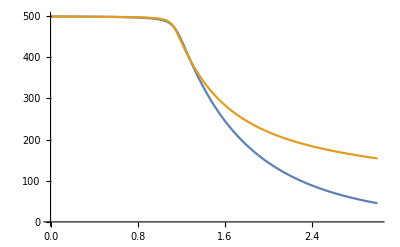

```mathematica
(* Residual population size *)
ListLinePlot[{datFastLow[[;;,{1,2}]],datFastLow[[;;,{1,3}]]}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Fast_low.csv",datFastLow]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Fast_low.csv

## Second : show one archetypal set of curves

```mathematica
i = 2;
qFlux=NDSolve[Flatten[{sirFlux,
{S1[0]==n1-1,S2[0]==n2-1,I1[0]==1,I2[0]==1,R1[0]==0,R2[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->0.5},
Flatten[{stvec,itvec,rtvec}],
{t,0,10000}];
qTar = NDSolve[Flatten[{sirTar,
{s11[0]==n1-1,s12[0]==0,s22[0]==n2-1,s21[0]==0,
i11[0]==1,i12[0]==0,i22[0]==1,i21[0]==0,
r11[0]==0,r12[0]==0,r22[0]==0,r21[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->0.5},
TarVars,
{t,0,10000}];
```

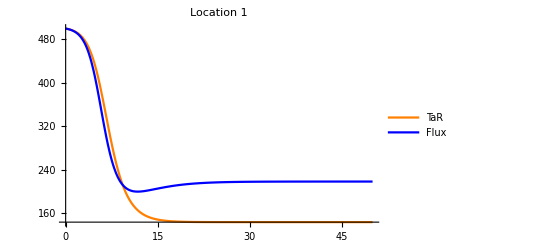

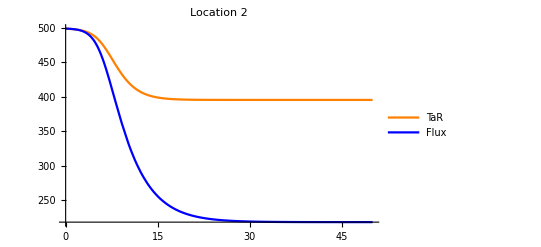

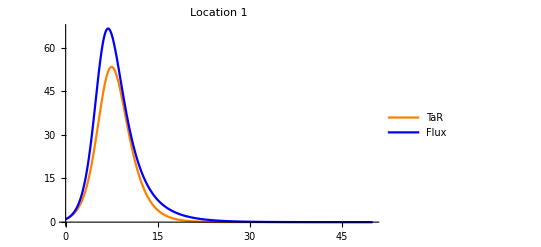

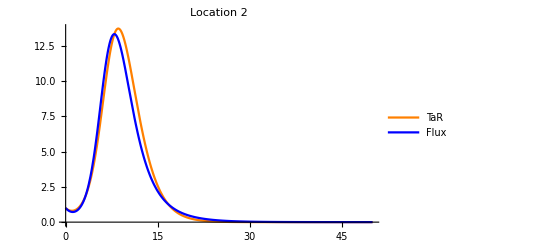

```mathematica
Plot[{(s11[t]+s12[t])/.qTar,S1[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 1",PlotLegends->{"TaR","Flux"}]
Plot[{(s22[t]+s21[t])/.qTar,S2[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 2",PlotLegends->{"TaR","Flux"}]

Plot[{(i11[t]+i12[t])/.qTar,I1[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 1",PlotLegends->{"TaR","Flux"}]
Plot[{(i22[t]+i21[t])/.qTar,I2[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 2",PlotLegends->{"TaR","Flux"}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Fast_low_time_series.csv",Table[{t,(s11[t]+s12[t])/.qTar[[1]],S1[t]/.qFlux[[1]],(i11[t]+i12[t])/.qTar[[1]],I1[t]/.qFlux[[1]]},{t,0,60,.25}]]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Fast_low_time_series.csv

# (Lower Left) Low Freq Travel; High L2 Β

```mathematica
poppars={n1->500.,n2->500.};
sirpars={γ->1.};
(* High Frequency Travel *) 
tarpars=    {ϕ1->1/100, τ12 ->10/100,ϕ2->1/100,τ21 ->10/100};
```

## First : solve for residual population size as a function of β

```mathematica
datSlowHigh =Table[qFlux=NDSolve[Flatten[{sirFlux,
{S1[0]==n1-1,S2[0]==n2-1,I1[0]==1,I2[0]==1,R1[0]==0,R2[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->2.5},
Flatten[{stvec,itvec,rtvec}],
{t,0,10000}];
qTar = NDSolve[Flatten[{sirTar,
{s11[0]==n1-1,s12[0]==0,s22[0]==n2-1,s21[0]==0,
i11[0]==1,i12[0]==0,i22[0]==1,i21[0]==0,
r11[0]==0,r12[0]==0,r22[0]==0,r21[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->2.5},
TarVars,
{t,0,10000}];
{i,(s11[t]+s12[t])/.qTar[[1]]/.t->10000,S1[t]/.qFlux[[1]]/.t->10000},
{i,0,3,.01}];
```

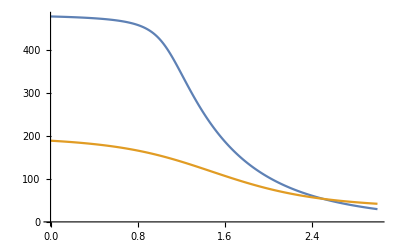

```mathematica
(* Residual population size *)
ListLinePlot[{datSlowHigh[[;;,{1,2}]],datSlowHigh[[;;,{1,3}]]}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Slow_high.csv",datSlowHigh]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Slow_high.csv

## Second : show one archetypal set of curves

```mathematica
i = 1.5;
qFlux=NDSolve[Flatten[{sirFlux,
{S1[0]==n1-1,S2[0]==n2-1,I1[0]==1,I2[0]==1,R1[0]==0,R2[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->2.5},
Flatten[{stvec,itvec,rtvec}],
{t,0,10000}];
qTar = NDSolve[Flatten[{sirTar,
{s11[0]==n1-1,s12[0]==0,s22[0]==n2-1,s21[0]==0,
i11[0]==1,i12[0]==0,i22[0]==1,i21[0]==0,
r11[0]==0,r12[0]==0,r22[0]==0,r21[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->2.5},
TarVars,
{t,0,10000}];
```

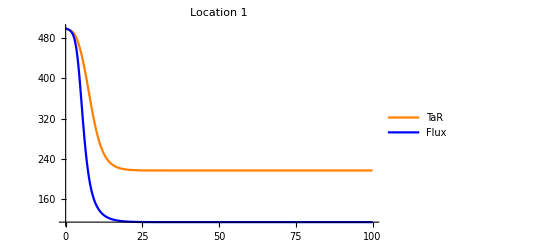

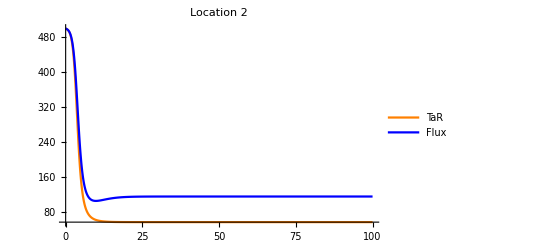

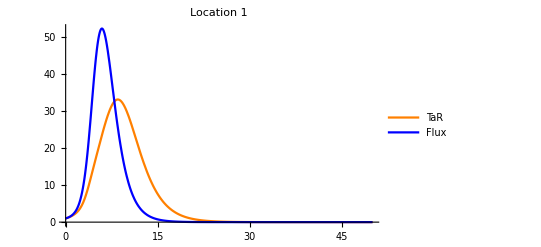

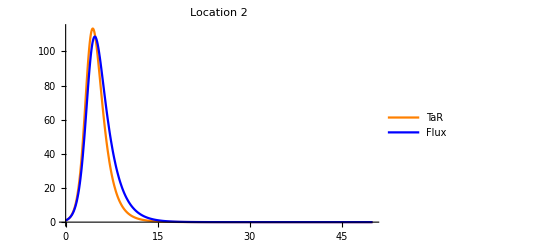

```mathematica
Plot[{(s11[t]+s12[t])/.qTar,S1[t]/.qFlux},{t,0,100},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 1",PlotLegends->{"TaR","Flux"}]
Plot[{(s22[t]+s21[t])/.qTar,S2[t]/.qFlux},{t,0,100},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 2",PlotLegends->{"TaR","Flux"}]

Plot[{(i11[t]+i12[t])/.qTar,I1[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 1",PlotLegends->{"TaR","Flux"}]
Plot[{(i22[t]+i21[t])/.qTar,I2[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 2",PlotLegends->{"TaR","Flux"}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Slow_high_time_series.csv",Table[{t,(s11[t]+s12[t])/.qTar[[1]],S1[t]/.qFlux[[1]],(i11[t]+i12[t])/.qTar[[1]],I1[t]/.qFlux[[1]]},{t,0,60,.25}]]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Slow_high_time_series.csv

# (Lower Right) Low Freq Travel; Low L2 Β

```mathematica
poppars={n1->500.,n2->500.};
sirpars={γ->1.};
(* High Frequency Travel *) 
tarpars=  {ϕ1->1/100, τ12 ->10/100,ϕ2->1/100,τ21 ->10/100};
```

## First : solve for residual population size as a function of β

```mathematica
datFastLow =Table[qFlux=NDSolve[Flatten[{sirFlux,
{S1[0]==n1-1,S2[0]==n2-1,I1[0]==1,I2[0]==1,R1[0]==0,R2[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->0.5},
Flatten[{stvec,itvec,rtvec}],
{t,0,10000}];
qTar = NDSolve[Flatten[{sirTar,
{s11[0]==n1-1,s12[0]==0,s22[0]==n2-1,s21[0]==0,
i11[0]==1,i12[0]==0,i22[0]==1,i21[0]==0,
r11[0]==0,r12[0]==0,r22[0]==0,r21[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->0.5},
TarVars,
{t,0,10000}];
{i,(s11[t]+s12[t])/.qTar[[1]]/.t->10000,S1[t]/.qFlux[[1]]/.t->10000},
{i,0,3,.01}];
```

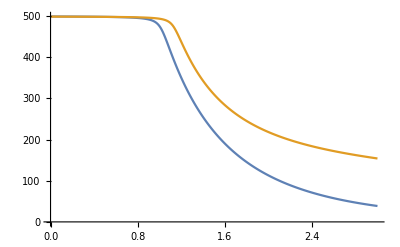

```mathematica
(* Residual population size *)
ListLinePlot[{datFastLow[[;;,{1,2}]],datFastLow[[;;,{1,3}]]}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Slow_low.csv",datFastLow]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Slow_low.csv

## Second : show one archetypal set of curves

```mathematica
i = 2;
qFlux=NDSolve[Flatten[{sirFlux,
{S1[0]==n1-1,S2[0]==n2-1,I1[0]==1,I2[0]==1,R1[0]==0,R2[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->0.5},
Flatten[{stvec,itvec,rtvec}],
{t,0,10000}];
qTar = NDSolve[Flatten[{sirTar,
{s11[0]==n1-1,s12[0]==0,s22[0]==n2-1,s21[0]==0,
i11[0]==1,i12[0]==0,i22[0]==1,i21[0]==0,
r11[0]==0,r12[0]==0,r22[0]==0,r21[0]==0}}]/.poppars/.sirpars/.tarpars/.fluxpars/.{β1->i,β2->0.5},
TarVars,
{t,0,10000}];
```

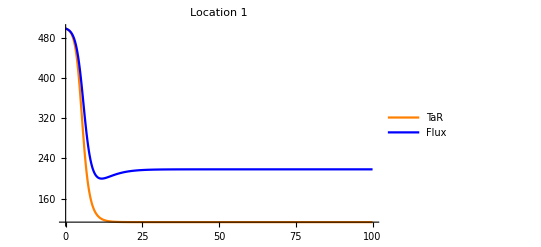

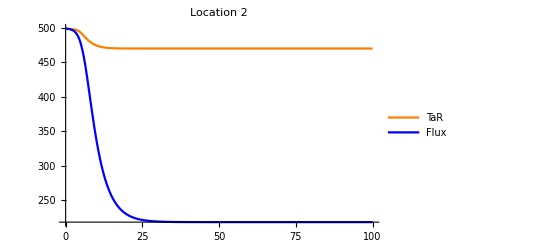

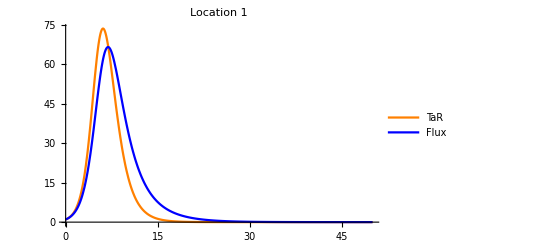

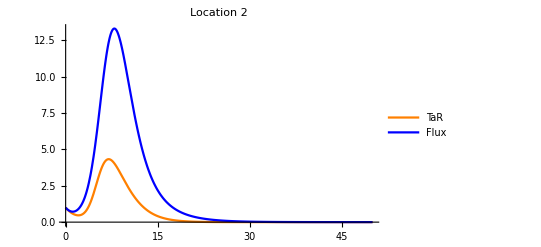

```mathematica
Plot[{(s11[t]+s12[t])/.qTar,S1[t]/.qFlux},{t,0,100},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 1",PlotLegends->{"TaR","Flux"}]
Plot[{(s22[t]+s21[t])/.qTar,S2[t]/.qFlux},{t,0,100},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 2",PlotLegends->{"TaR","Flux"}]


Plot[{(i11[t]+i12[t])/.qTar,I1[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 1",PlotLegends->{"TaR","Flux"}]
Plot[{(i22[t]+i21[t])/.qTar,I2[t]/.qFlux},{t,0,50},PlotRange->Full,PlotStyle->{Orange,Blue},PlotLabel->"Location 2",PlotLegends->{"TaR","Flux"}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Slow_low_time_series.csv",Table[{t,(s11[t]+s12[t])/.qTar[[1]],S1[t]/.qFlux[[1]],(i11[t]+i12[t])/.qTar[[1]],I1[t]/.qFlux[[1]]},{t,0,60,.25}]]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/SIR_Slow_low_time_series.csv